```mathematica
allEdges[n_]:=Flatten[Table[UndirectedEdge[i,j],{i,1,n},{j,i+1,n}]];
allConnected[n_]:=Select[Map[Graph[Range[n],#,VertexLabels->Automatic]&,Subsets[allEdges[n]]],ConnectedGraphQ];
allConnectedUpToIso[n_]:=DeleteDuplicates[allConnected[n],IsomorphicGraphQ];
vertex5=allConnectedUpToIso[5];
(*vertex6=allConnectedUpToIso[6];*)
```

```mathematica
PerfectDistanceQ[G_]:=Union[Flatten[Round[GraphDistanceMatrix[G]]]] == Range[0,Binomial[VertexCount[G],2]]
WeightsList[G_]:=Flatten[Permutations[#]&/@Select[Subsets[Range[Binomial[VertexCount[G],2]],{EdgeCount[G]}],MemberQ[#,1]&&MemberQ[#,2]&],1]
```

```mathematica
AbsoluteTiming[
G=vertex5[[7]];

WL = WeightsList[G]; 
WeightedGraphs=Graph[EdgeList[G],EdgeWeight->#]&/@WL;
PerfectDistanceGraphTable =PerfectDistanceQ[#]&/@WeightedGraphs;
PerfectDistanceGraphs=Pick[WeightedGraphs,PerfectDistanceGraphTable];
]

AutG= GraphAutomorphismGroup[G];
Length[PerfectDistanceGraphs]
GroupOrder[AutG]
Length[PerfectDistanceGraphs]/GroupOrder[AutG]
```

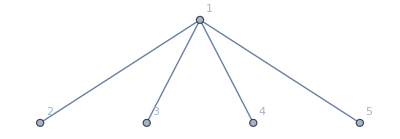
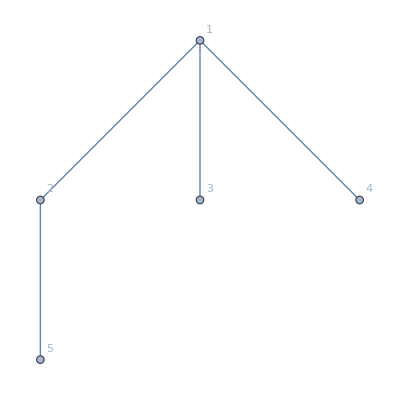
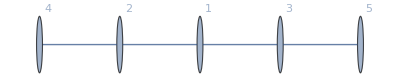
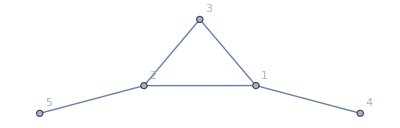
{Null,{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
GraphList = vertex5;
MinimalPerfectDistanceGraphs = {};

Reap[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];
WL = WeightsList[G];
PerfectDistanceGraph = Catch[Do[If[PerfectDistanceQ[Graph[EdgeList[G],EdgeWeight->WL[[j]]]],Throw[G]],{j,1,Length[WL]}]];
If[PerfectDistanceGraph==Null,Sow[G]];
AppendTo[MinimalPerfectDistanceGraphs,PerfectDistanceGraph];
MinimalPerfectDistanceGraphs = DeleteCases[MinimalPerfectDistanceGraphs,Null];
GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[PerfectDistanceGraph,#]]&]
]
]
```